# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\quantum_chaotic_channels\MG files\enviroment state dependence\single random excitation in caometer and enviroment

```mathematica
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\QMB.wl"]
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\Chaometer.wl"]
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
Clear[haar];
haar[dim_Integer]:=Module[{l=2^dim,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
(*Define the Pauli matrices*)
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
(*Define collective spin operators for n spins*)
Clear[Jx,Jy,Jz];
Jx[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sx,IdentityMatrix[2]],{j,n}],{i,n}];
Jy[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sy,IdentityMatrix[2]],{j,n}],{i,n}];
Jz[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sz,IdentityMatrix[2]],{j,n}],{i,n}];
(*Define the Lipkin Hamiltonian*)
Clear[Hlmg];
Hlmg[α_,gx_,gy_,n_]:=α*Jz[n]+(gx/(n-1))(Jx[n].Jx[n])+(gy/(n-1))(Jy[n].Jy[n]);
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

### Ensemble of initial states ψ_s ⊗ ψ_e, Chaotic

# Wisniacki chain

## Hamiltonian

```mathematica
L=5;
hx=J=1.;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ale=50;
caometer=Table[haar[1],{i,ale}];
ψTa=Table[haar[L-1],{i,ale}];
(*ψTb=Table[Normalize[Table[Exp[i*I*RandomReal[]],{i,2^(L-1)}]],{i,ale}];*)
(*ψTb=Table[coherentstate[caometer[[i]],L-1],{i,ale}];*)
ψTb=Table[Normalize[ConstantArray[1,L-1]],{i,ale}];
ψTc=Table[RandomChainProductState[L-1],{i,ale}];
```

```mathematica
ψa=ArrayReshape[ParallelTable[Flatten[KroneckerProduct[i,j]],{j,ψTa},{i,caometer}],{ale*ale,2^L}];
ψb=ArrayReshape[ParallelTable[Flatten[KroneckerProduct[i,j]],{j,ψTb},{i,caometer}],{ale*ale,2^L}];
ψc=ArrayReshape[ParallelTable[Flatten[KroneckerProduct[i,j]],{j,ψTc},{i,caometer}],{ale*ale,2^L}];
```

```mathematica
eigenψa=ParallelTable[Conjugate[eigenvec].i,{i,ψa}];
eigenψb=ParallelTable[Conjugate[eigenvec].i,{i,ψb}];
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
iprsb=ParallelTable[Total[Abs[i]^4],{i,eigenψb}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
energiesa=Table[Chop[Conjugate[i].H.i],{i,ψa}];
energiesb=Table[Chop[Conjugate[i].H.i],{i,ψb}];
energiesc=Table[Chop[Conjugate[i].H.i],{i,ψc}];
```

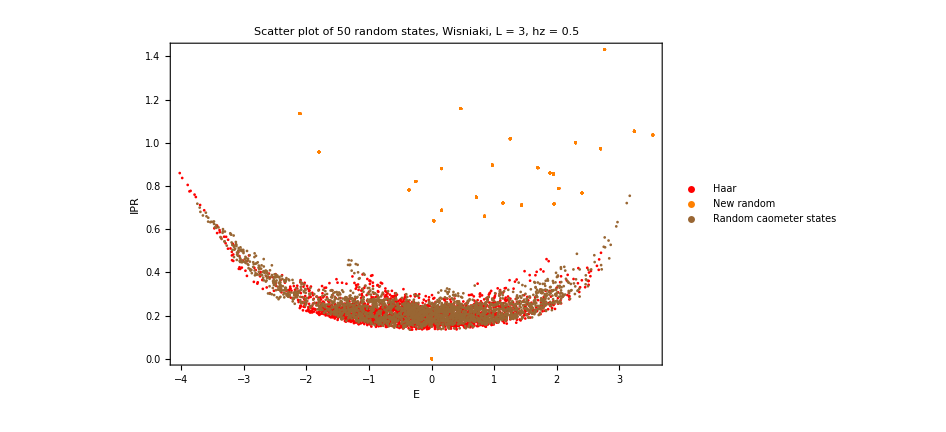

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
```

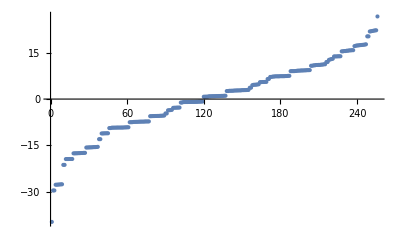

```mathematica
ListPlot[eigenval,PlotRange->All]
```

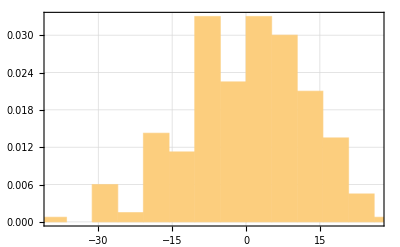

```mathematica
(*Define energy range and bin width*){emin,emax}={Min[eigenval],Max[eigenval]};
binWidth=20*Mean[Differences[Sort[eigenval+Min[eigenval]]]];
(*Create histogram bins for density of states*)
DOS=Histogram[eigenval,{binWidth},"ProbabilityDensity",PlotRange->{{emin,emax},All},PlotTheme->"Detailed",PlotRange->All]
```

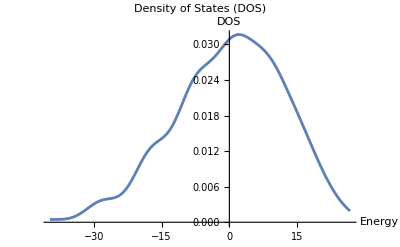

```mathematica
(*Kernel Density Estimate for smoother DOS*)dosDensity=SmoothKernelDistribution[eigenval];
(*Plot the smoothed density of states*)
Plot[PDF[dosDensity,e],{e,emin,emax},PlotLabel->"Density of States (DOS)",AxesLabel->{"Energy","DOS"}]
```

```mathematica
ipreigen=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
```

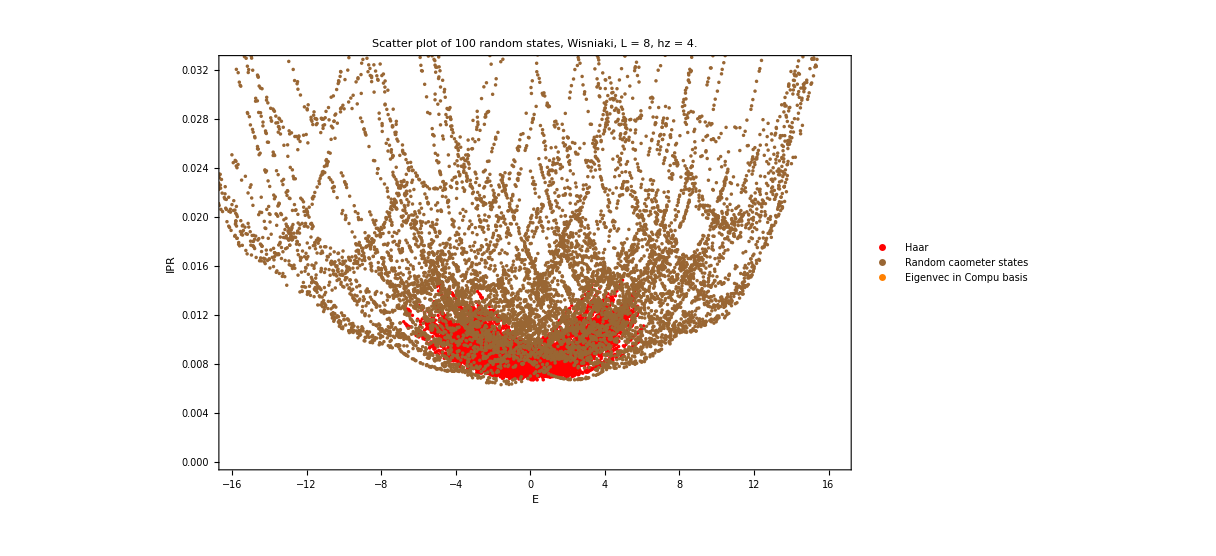

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesc,iprsc}],Transpose[{eigenval,ipreigen}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Brown,Orange},PlotLegends->{Style["Haar",Red],Style["Random caometer states",Brown],Style["Eigenvec in Compu basis",Orange]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]},ImageSize->900]
```

```mathematica
iprsa=ParallelTable[Total[Abs[i]^4],{i,ψa}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,ψc}];
```

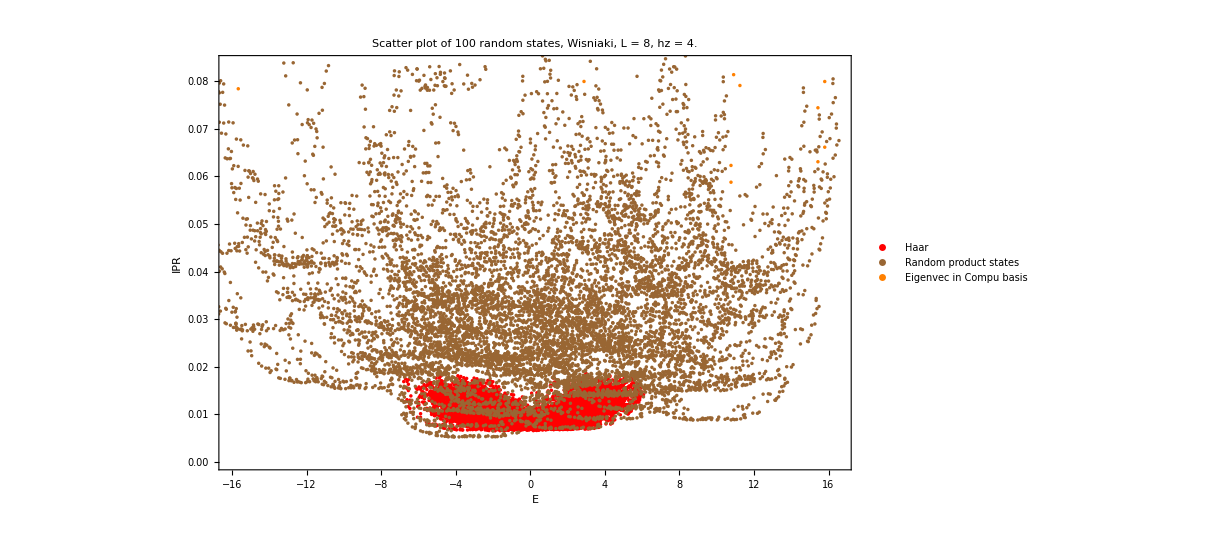

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesc,iprsc}],Transpose[{eigenval,ipreigen}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Brown,Orange},PlotLegends->{Style["Haar",Red],Style["Random product states",Brown],Style["Eigenvec in Compu basis",Orange]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]},ImageSize->900]
```

```mathematica
ale=50;
caometer=Table[haar[1],{i,ale}];
ψTa=Table[haar[L-1],{i,ale}];
ψTc=Table[RandomChainProductState[L-1],{i,ale}];
```

```mathematica
ψa=ArrayReshape[ParallelTable[Flatten[KroneckerProduct[i,j]],{j,ψTa},{i,caometer}],{ale*ale,2^L}];
ψc=ArrayReshape[ParallelTable[Flatten[KroneckerProduct[i,j]],{j,ψTc},{i,caometer}],{ale*ale,2^L}];
```

```mathematica
energiesa=ParallelTable[Chop[Conjugate[i].H.i],{i,ψa}];
energiesc=ParallelTable[Chop[Conjugate[i].H.i],{i,ψc}];
```

```mathematica
ListPlot[eigenval,PlotRange->All]
```

-Graphics-

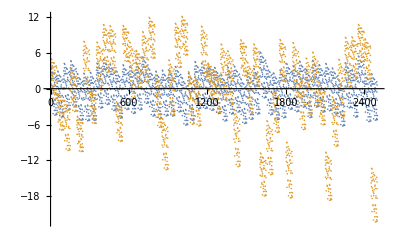

```mathematica
ListPlot[{energiesa,energiesc},PlotRange->All]
```

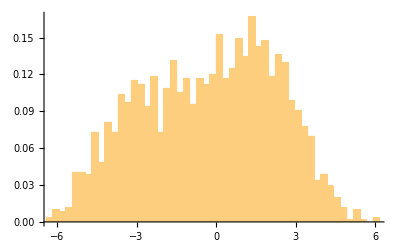

```mathematica
(*Define energy range and bin width*){emin,emax}={Min[energiesa],Max[energiesa]};
binWidth=50*Mean[Differences[Sort[energiesa+Min[energiesa]]]];
(*Create histogram bins for density of states*)
dosHistograma=Histogram[energiesa,{binWidth},"ProbabilityDensity",PlotRange->{{emin,emax},All}]
```

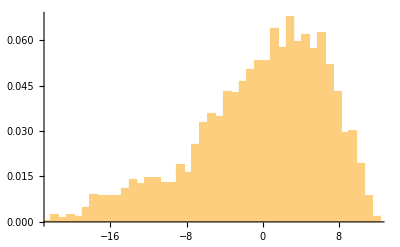

```mathematica
(*Define energy range and bin width*){emin,emax}={Min[energiesc],Max[energiesc]};
binWidth=60*Mean[Differences[Sort[energiesc+Min[energiesc]]]];
(*Create histogram bins for density of states*)
dosHistogramc=Histogram[energiesc,{binWidth},"ProbabilityDensity",PlotRange->{{emin,emax},All}]
```

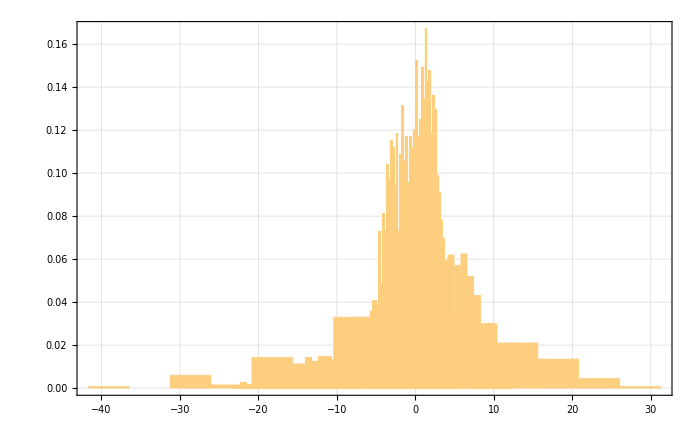

```mathematica
Show[{DOS, dosHistograma, dosHistogramc},PlotRange->All,ImageSize->700]
```

```mathematica
(*Find positions of elements within the range-2 to 2*)
positionsa=Position[energiesa,x_/;-3<=x<=3];
positionsc=Position[energiesc,x_/;-3<=x<=3];
```

```mathematica
eigenψa=Table[Conjugate[eigenvec].ψa[[i]],{i,Flatten[positionsa]}];
eigenψc=Table[Conjugate[eigenvec].ψc[[i]],{i,Flatten[positionsc]}];
```

```mathematica
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
```

## Magnetization and SP(t)

```mathematica
ope=Jz[L];
maga=Table[Chop[Conjugate[i].ope.i],{i,ψa}];
magb=Table[Chop[Conjugate[i].ope.i],{i,ψb}];
magc=Table[Chop[Conjugate[i].ope.i],{i,ψc}];
ope2=Jz[L].Jz[L];
maga=Table[Chop[Conjugate[i].ope.i],{i,ψa}];
magb=Table[Chop[Conjugate[i].ope.i],{i,ψb}];
magc=Table[Chop[Conjugate[i].ope.i],{i,ψc}];
vara=Table[Chop[Conjugate[ψa[[i]]].ope2.ψa[[i]]]-maga[[i]],{i,Length[ψa]}];
varb=Table[Chop[Conjugate[ψb[[i]]].ope2.ψb[[i]]]-magb[[i]],{i,Length[ψb]}];
varc=Table[Chop[Conjugate[ψc[[i]]].ope2.ψc[[i]]]-magc[[i]],{i,Length[ψc]}];
```

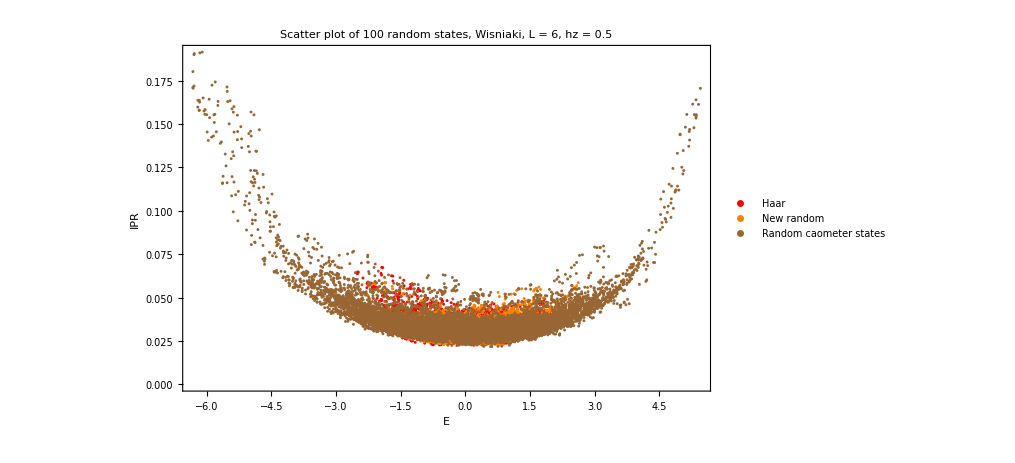

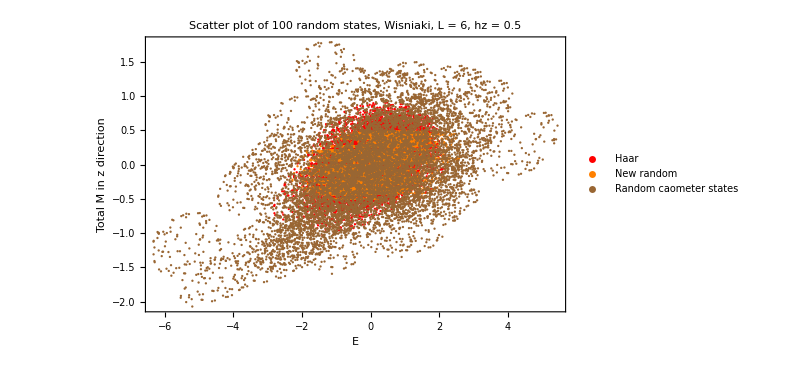

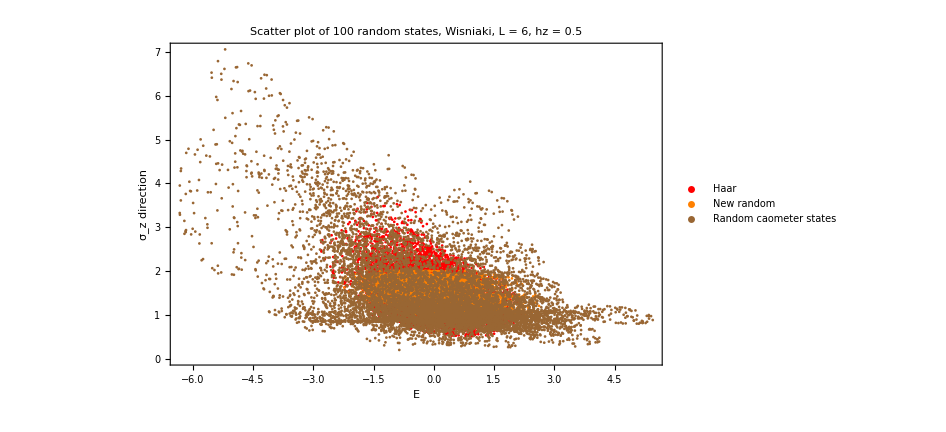

```mathematica
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["Total M in z direction"]}]
ListPlot[{Transpose[{energiesa,vara}],Transpose[{energiesb,varb}],Transpose[{energiesc,varc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["σ_z direction"]}]
```

```mathematica
ψat=Table[StateEvolution[t,ψa[[1]],eigenval,eigenvec],{t,0,50,0.1}];
ψbt=Table[StateEvolution[t,ψb[[1]],eigenval,eigenvec],{t,0,50,0.1}];
ψct=Table[StateEvolution[t,ψc[[1]],eigenval,eigenvec],{t,0,50,0.1}];
```

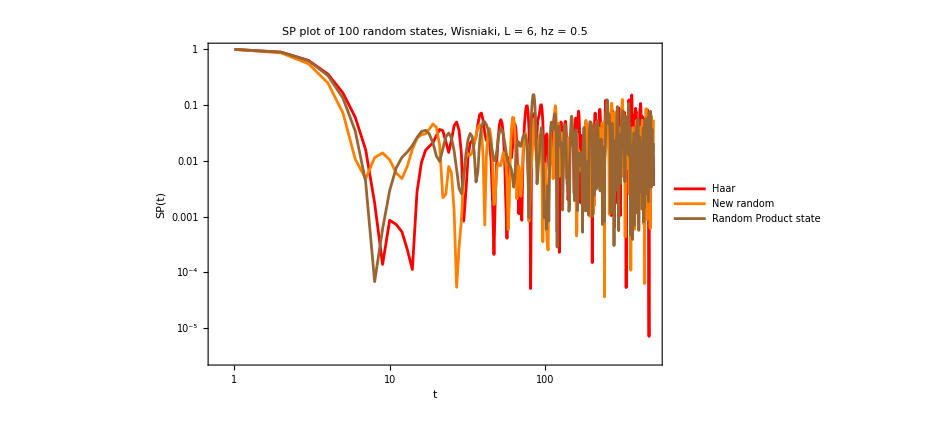

```mathematica
ListLogLogPlot[{Table[Abs[Conjugate[ψa[[1]]].i]^2,{i,ψat}],Table[Abs[Conjugate[ψb[[1]]].i]^2,{i,ψbt}],Table[Abs[Conjugate[ψc[[1]]].i]^2,{i,ψct}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["SP plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

```mathematica
densitya=Table[Dyad[i,i],{i,ψat}];
densityb=Table[Dyad[i,i],{i,ψbt}];
densityc=Table[Dyad[i,i],{i,ψct}];
```

```mathematica
reduceda=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densitya}];
reducedb=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityb}];
reducedc=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityc}];
```

```mathematica
puritiesa=ParallelTable[Chop[Purity[i]],{i,reduceda}];
puritiesb=ParallelTable[Chop[Purity[i]],{i,reducedb}];
puritiesc=ParallelTable[Chop[Purity[i]],{i,reducedc}];
```

```mathematica
tlist=Range[0,50,0.1];
```

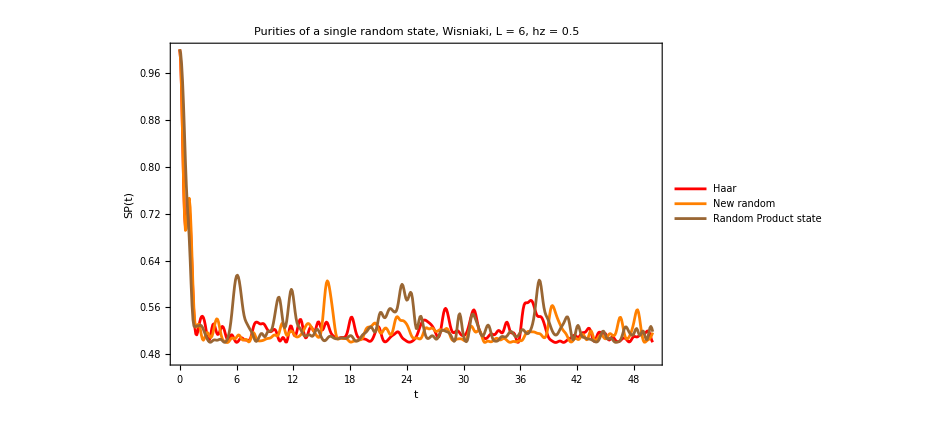

```mathematica
ListPlot[{Transpose[{tlist,puritiesa}],Transpose[{tlist,puritiesb}],Transpose[{tlist,puritiesc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]},PlotRange->All]
```

```mathematica
reducedmagax=Table[Chop[Tr[sx.i]],{i,reduceda}];
reducedmagay=Table[Chop[Tr[sy.i]],{i,reduceda}];
reducedmagaz=Table[Chop[Tr[sz.i]],{i,reduceda}];
reducedmagbx=Table[Chop[Tr[sx.i]],{i,reducedb}];
reducedmagby=Table[Chop[Tr[sy.i]],{i,reducedb}];
reducedmagbz=Table[Chop[Tr[sz.i]],{i,reducedb}];
reducedmagcx=Table[Chop[Tr[sx.i]],{i,reducedc}];
reducedmagcy=Table[Chop[Tr[sy.i]],{i,reducedc}];
reducedmagcz=Table[Chop[Tr[sz.i]],{i,reducedc}];
```

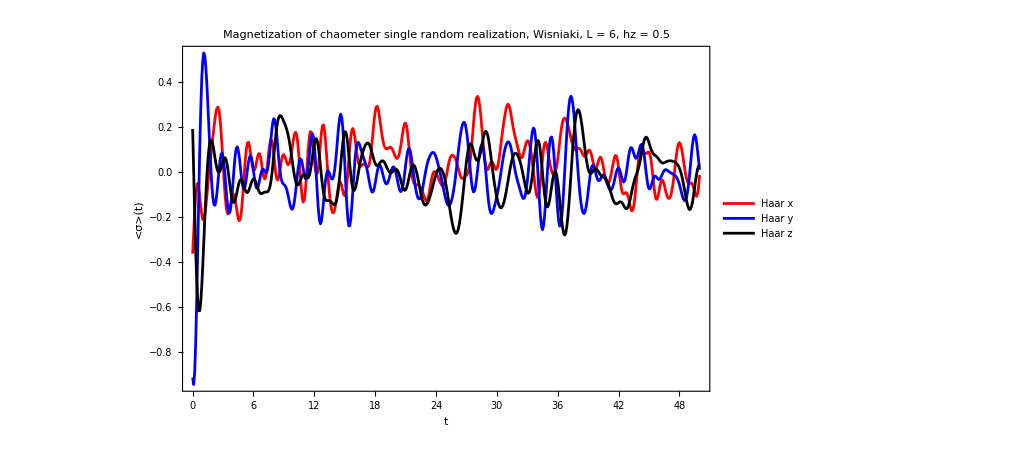

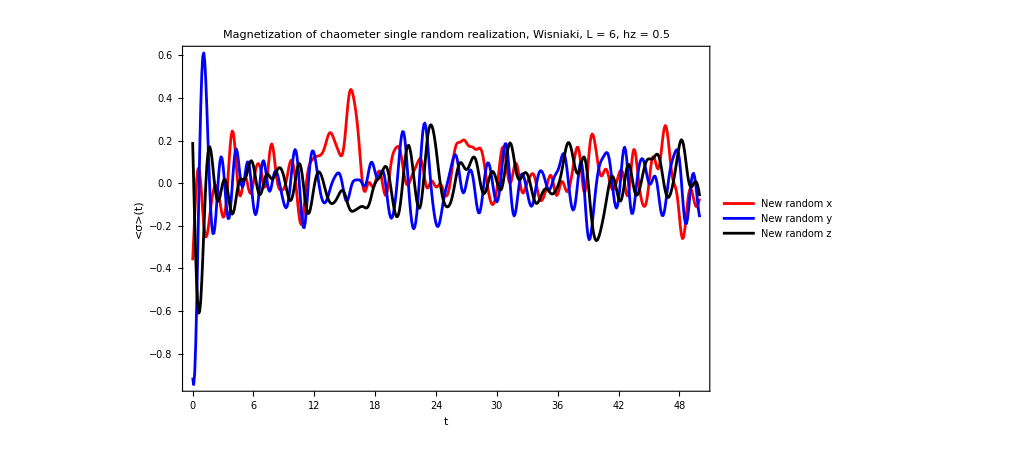

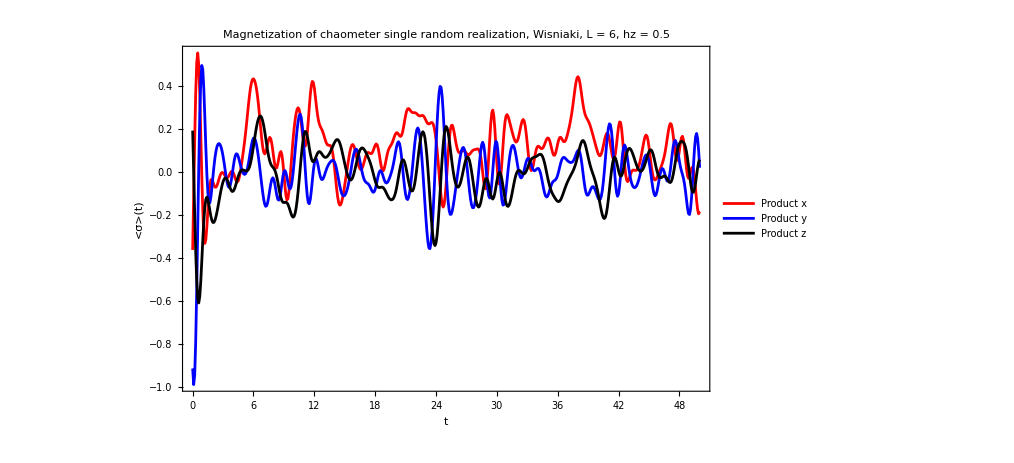

```mathematica
ListPlot[{Transpose[{tlist,reducedmagax}],Transpose[{tlist,reducedmagay}],Transpose[{tlist,reducedmagaz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of chaometer single random realization, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Directive[Red],Directive[Blue],Directive[Black]},ImageSize->750,PlotLegends->{Style["Haar x",Red],Style["Haar y",Blue],Style["Haar z",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]},PlotRange->All]

ListPlot[{Transpose[{tlist,reducedmagbx}],Transpose[{tlist,reducedmagby}],Transpose[{tlist,reducedmagbz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of chaometer single random realization, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Directive[Red],Directive[Blue],Directive[Black]},ImageSize->750,PlotLegends->{Style["New random x",Red],Style["New random y",Blue],Style["New random z",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]},PlotRange->All]

ListPlot[{Transpose[{tlist,reducedmagcx}],Transpose[{tlist,reducedmagcy}],Transpose[{tlist,reducedmagcz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of chaometer single random realization, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Directive[Red],Directive[Blue],Directive[Black]},ImageSize->750,PlotLegends->{Style["Product x",Red],Style["Product y",Blue],Style["Product z",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]},PlotRange->All]
```

```mathematica
testplot=-Graphics-
```

-Graphics-

```mathematica
Export["randomstates_sizeL.png",testplot,ImageSize->1000,ImageResolution->300]
```

randomstates_sizeL.png

## Regular

```mathematica
L=5;
hx=J=1.;
hz=4.0;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
caometer=Table[haar[1],{i,50}];
```

```mathematica
ψa=Table[Flatten[KroneckerProduct[i,haar[L-1]]],{i,caometer}];
ψb=Table[Flatten[KroneckerProduct[i,Normalize[Table[Exp[i*I*RandomReal[]],{i,2^(L-1)}]]]],{i,caometer}];
ψc=Table[Flatten[KroneckerProduct[i,RandomChainProductState[L-1]]],{i,caometer}];
```

```mathematica
eigenψa=ParallelTable[Conjugate[eigenvec].i,{i,ψa}];
eigenψb=ParallelTable[Conjugate[eigenvec].i,{i,ψb}];
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
```

```mathematica
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
iprsb=ParallelTable[Total[Abs[i]^4],{i,eigenψb}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
```

```mathematica
energiesa=Table[Chop[Conjugate[i].H.i],{i,ψa}];
energiesb=Table[Chop[Conjugate[i].H.i],{i,ψb}];
energiesc=Table[Chop[Conjugate[i].H.i],{i,ψc}];
```

```mathematica
ope=Jz[L];
```

```mathematica
maga=Table[Chop[Conjugate[i].ope.i],{i,ψa}];
magb=Table[Chop[Conjugate[i].ope.i],{i,ψb}];
magc=Table[Chop[Conjugate[i].ope.i],{i,ψc}];
```

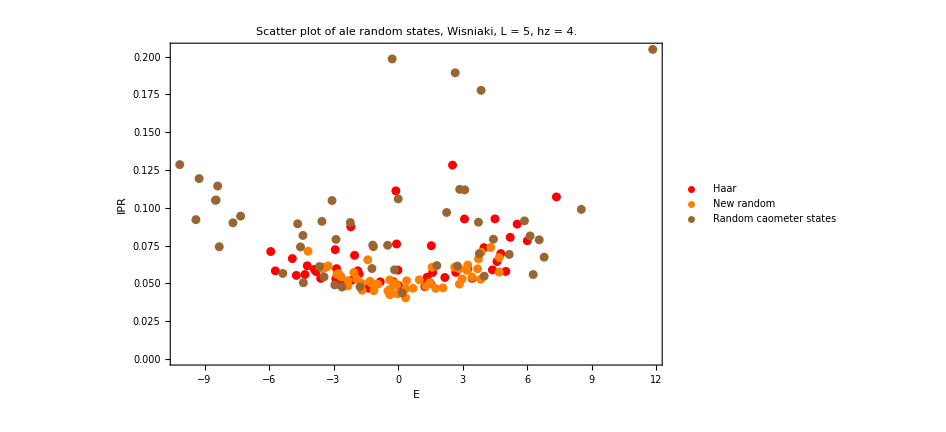

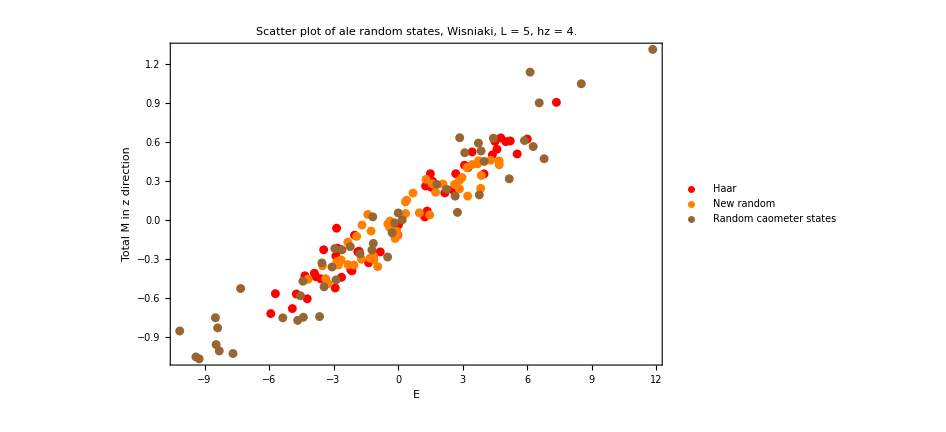

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["Total M in z direction"]}]
```

```mathematica
ψat=Table[StateEvolution[t,ψa[[1]],eigenval,eigenvec],{t,0,50,0.1}];
ψbt=Table[StateEvolution[t,ψb[[1]],eigenval,eigenvec],{t,0,50,0.1}];
ψct=Table[StateEvolution[t,ψc[[1]],eigenval,eigenvec],{t,0,50,0.1}];
```

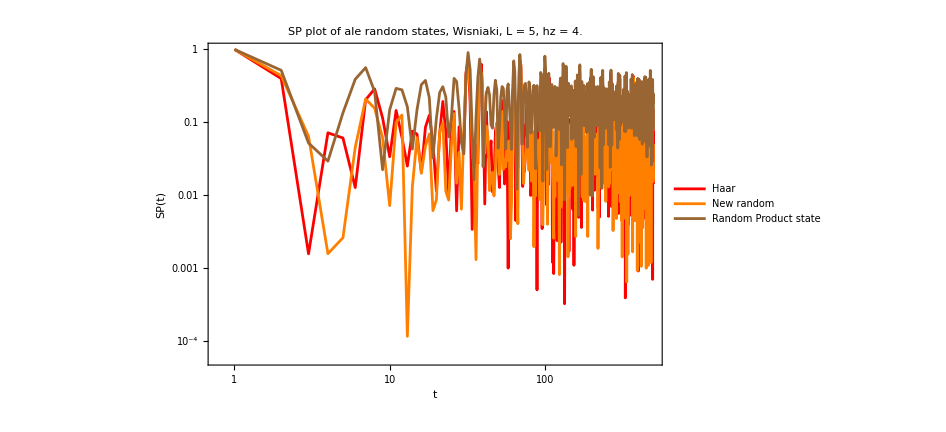

```mathematica
ListLogLogPlot[{Table[Abs[Conjugate[ψa[[1]]].i]^2,{i,ψat}],Table[Abs[Conjugate[ψb[[1]]].i]^2,{i,ψbt}],Table[Abs[Conjugate[ψc[[1]]].i]^2,{i,ψct}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["SP plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

```mathematica
densitya=ParallelTable[Dyad[i,i],{i,ψat}];
densityb=ParallelTable[Dyad[i,i],{i,ψbt}];
densityc=ParallelTable[Dyad[i,i],{i,ψct}];
```

```mathematica
reduceda=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densitya}];
reducedb=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityb}];
reducedc=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityc}];
```

```mathematica
puritiesa=ParallelTable[Chop[Purity[i]],{i,reduceda}];
puritiesb=ParallelTable[Chop[Purity[i]],{i,reducedb}];
puritiesc=ParallelTable[Chop[Purity[i]],{i,reducedc}];
```

```mathematica
tlist=Range[0,50,0.1];
```

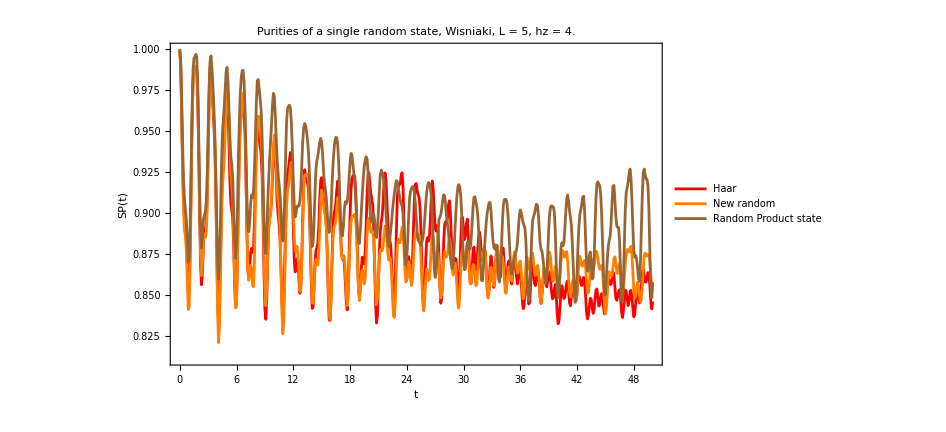

```mathematica
ListPlot[{Transpose[{tlist,puritiesa}],Transpose[{tlist,puritiesb}],Transpose[{tlist,puritiesc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]},PlotRange->All]
```

```mathematica
reducedmagax=Table[Chop[Tr[sx.i]],{i,reduceda}];
reducedmagay=Table[Chop[Tr[sy.i]],{i,reduceda}];
reducedmagaz=Table[Chop[Tr[sz.i]],{i,reduceda}];
reducedmagbx=Table[Chop[Tr[sx.i]],{i,reducedb}];
reducedmagby=Table[Chop[Tr[sy.i]],{i,reducedb}];
reducedmagbz=Table[Chop[Tr[sz.i]],{i,reducedb}];
reducedmagcx=Table[Chop[Tr[sx.i]],{i,reducedc}];
reducedmagcy=Table[Chop[Tr[sy.i]],{i,reducedc}];
reducedmagcz=Table[Chop[Tr[sz.i]],{i,reducedc}];
```

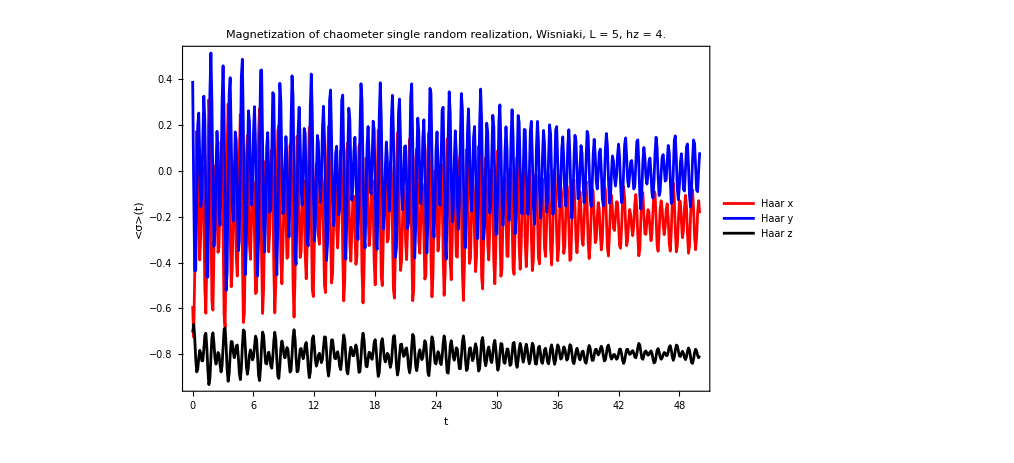

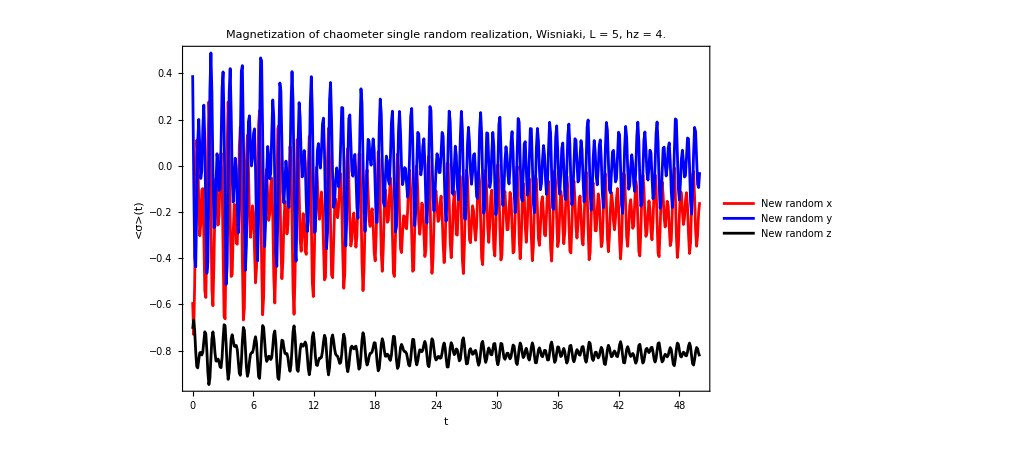

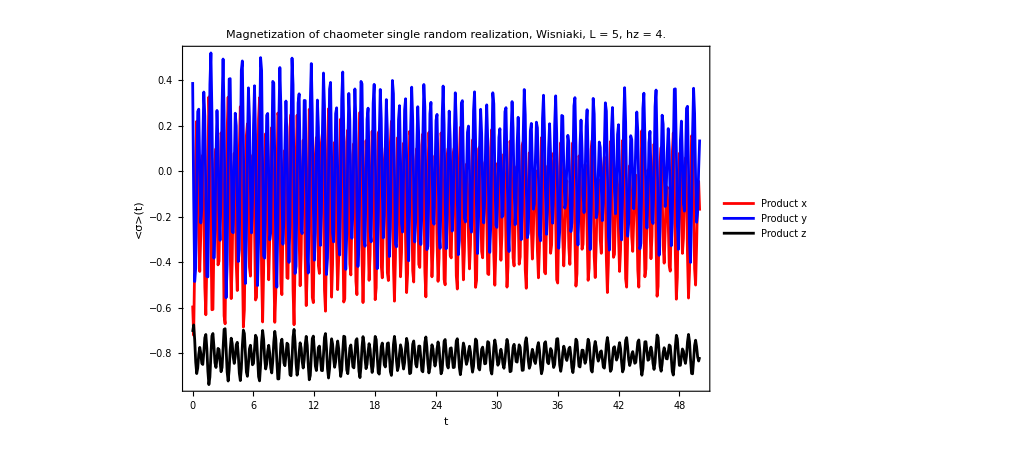

```mathematica
ListPlot[{Transpose[{tlist,reducedmagax}],Transpose[{tlist,reducedmagay}],Transpose[{tlist,reducedmagaz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of chaometer single random realization, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Directive[Red],Directive[Blue],Directive[Black]},ImageSize->750,PlotLegends->{Style["Haar x",Red],Style["Haar y",Blue],Style["Haar z",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]},PlotRange->All]

ListPlot[{Transpose[{tlist,reducedmagbx}],Transpose[{tlist,reducedmagby}],Transpose[{tlist,reducedmagbz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of chaometer single random realization, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Directive[Red],Directive[Blue],Directive[Black]},ImageSize->750,PlotLegends->{Style["New random x",Red],Style["New random y",Blue],Style["New random z",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]},PlotRange->All]

ListPlot[{Transpose[{tlist,reducedmagcx}],Transpose[{tlist,reducedmagcy}],Transpose[{tlist,reducedmagcz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of chaometer single random realization, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Directive[Red],Directive[Blue],Directive[Black]},ImageSize->750,PlotLegends->{Style["Product x",Red],Style["Product y",Blue],Style["Product z",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]},PlotRange->All]
```

## Random product states

```mathematica
L=9;
hx=J=1.;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ale=1000;
ψa=Table[haar[L],{i,ale}];
ψc=Table[RandomChainProductState[L],{i,ale}];
```

```mathematica
eigenψa=ParallelTable[Conjugate[eigenvec].i,{i,ψa}];
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
energiesa=Table[Chop[Conjugate[i].H.i],{i,ψa}];
energiesc=Table[Chop[Conjugate[i].H.i],{i,ψc}];
```

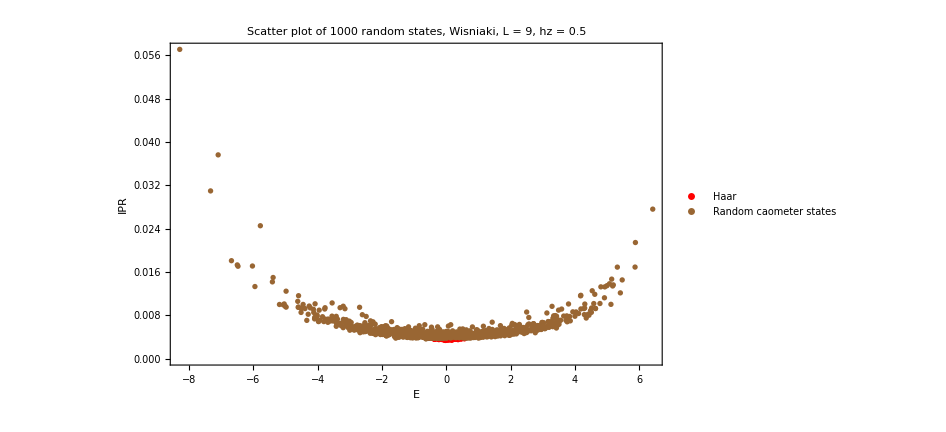

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
```

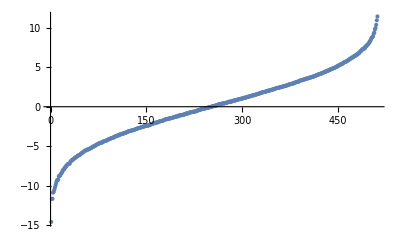

```mathematica
ListPlot[eigenval,PlotRange->All]
```

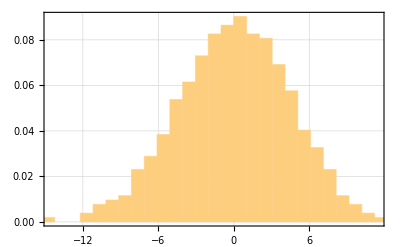

```mathematica
(*Define energy range and bin width*){emin,emax}={Min[eigenval],Max[eigenval]};
binWidth=20*Mean[Differences[Sort[eigenval+Min[eigenval]]]];
(*Create histogram bins for density of states*)
DOS=Histogram[eigenval,{binWidth},"ProbabilityDensity",PlotRange->{{emin,emax},All},PlotTheme->"Detailed",PlotRange->All]
```

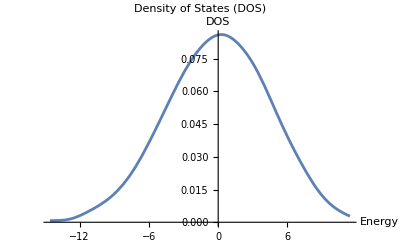

```mathematica
(*Kernel Density Estimate for smoother DOS*)dosDensity=SmoothKernelDistribution[eigenval];
(*Plot the smoothed density of states*)
Plot[PDF[dosDensity,e],{e,emin,emax},PlotLabel->"Density of States (DOS)",AxesLabel->{"Energy","DOS"}]
```

```mathematica
ipreigen=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
```

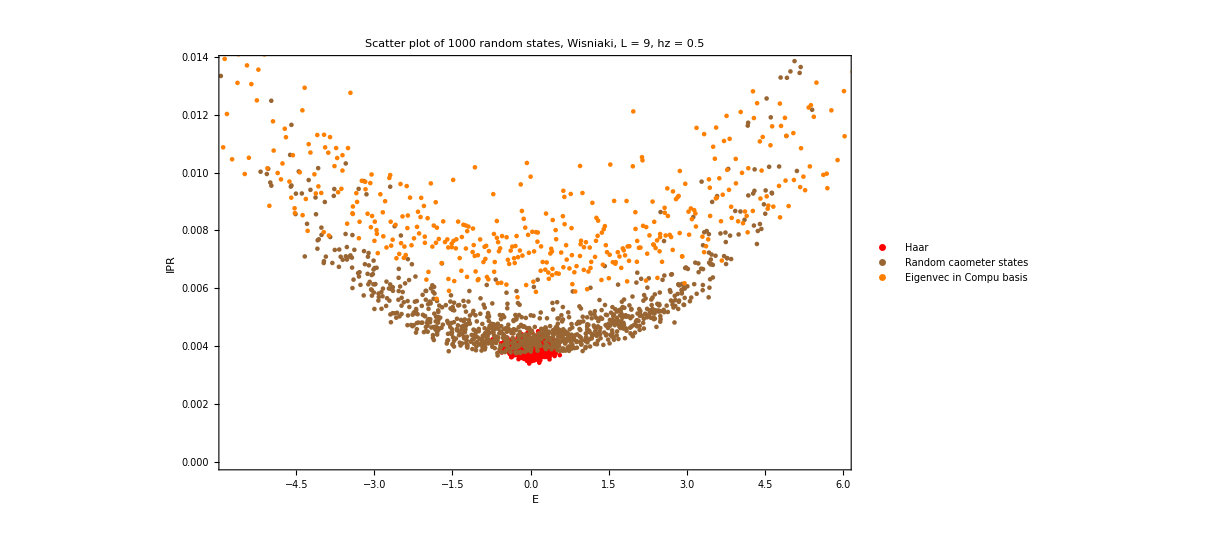

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesc,iprsc}],Transpose[{eigenval,ipreigen}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Brown,Orange},PlotLegends->{Style["Haar",Red],Style["Random caometer states",Brown],Style["Eigenvec in Compu basis",Orange]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]},ImageSize->900]
```

```mathematica
iprsa=ParallelTable[Total[Abs[i]^4],{i,ψa}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,ψc}];
```

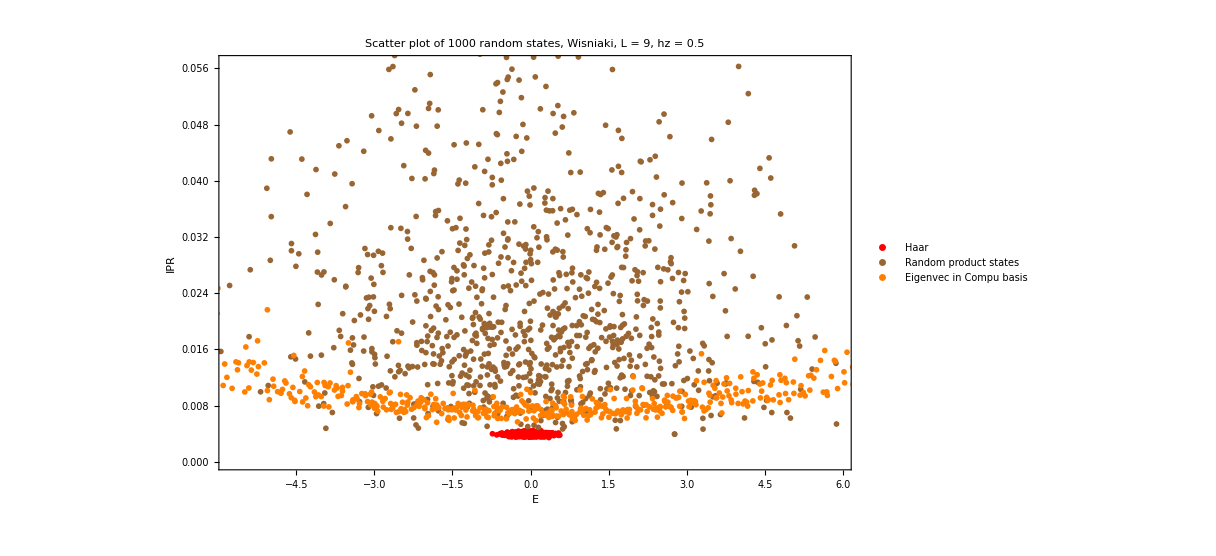

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesc,iprsc}],Transpose[{eigenval,ipreigen}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Brown,Orange},PlotLegends->{Style["Haar",Red],Style["Random product states",Brown],Style["Eigenvec in Compu basis",Orange]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]},ImageSize->900]
```

# Purities

```mathematica
L=5;
hx=1;
J=1.;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
(*L=5;
Δ=1.;
H=ClosedXXZHamiltonian[L,Δ];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];*)
ale2=30;
coloursc=Table[RGBColor[i,i/ale2,1-i],{i,ale2}];
blochtest=Table[qubit[Pi/2,i],{i,0,2Pi,2Pi/(ale2-1)}];
```

```mathematica
ψTa=coherentstate[qubit[0,0],L-1];
ψa=Table[Flatten[KroneckerProduct[ψTa,i]],{i,blochtest}];
eigenψa=ParallelTable[Conjugate[eigenvec].i,{i,ψa}];
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
energiesa=Table[Chop[Conjugate[i].H.i],{i,ψa}];
```

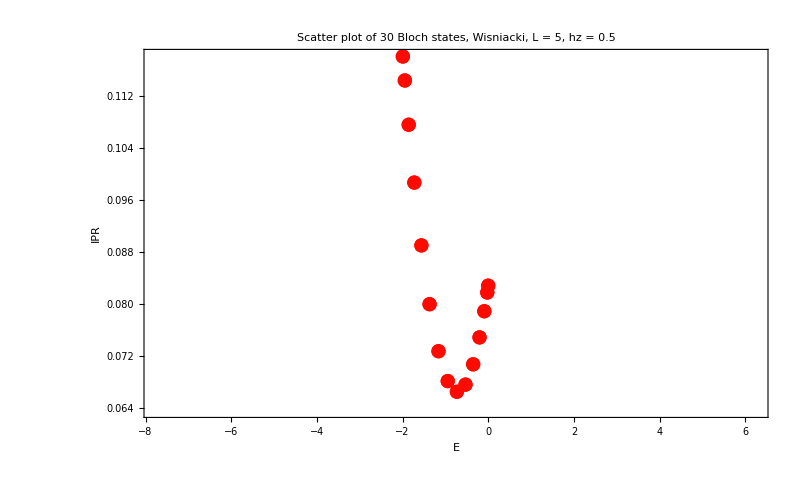

```mathematica
ListPlot[Transpose[{energiesa,iprsa}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale2]<>" Bloch states, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->coloursc[[1]],PlotRange->{{Min[eigenval],Max[eigenval]},All},ImageSize->800,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
```

```mathematica
tf=1.6;
dt=0.005;
tlist=Range[0,tf,dt];
ψat=Table[StateEvolution[t,j,eigenval,eigenvec],{j,ψa},{t,0,tf,dt}];
```

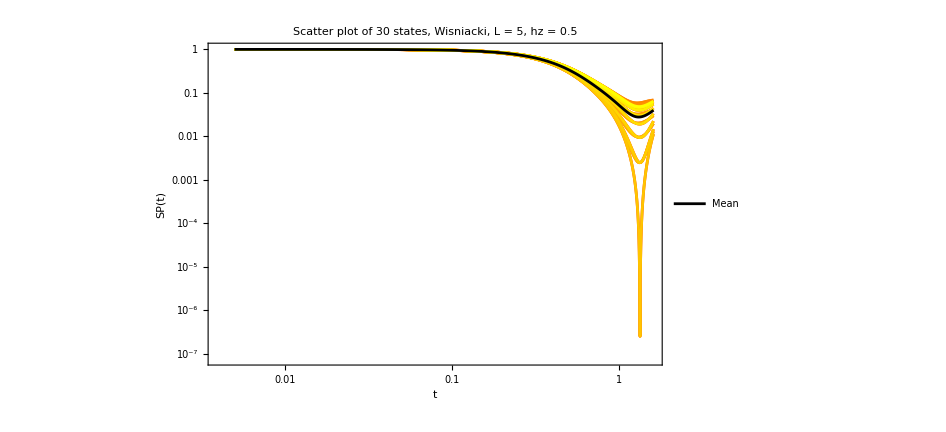

```mathematica
singlea=ListLogLogPlot[Table[{tlist[[i]],Abs[Conjugate[ψat[[j,1]]].ψat[[j,i]]]^2},{j,Length[ψat]},{i,Length[Range[0,tf,dt]]}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale2]<>" states, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->coloursc,PlotRange->All,ImageSize->700,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}];
meana=ListLogLogPlot[Mean[Table[{tlist[[i]],Abs[Conjugate[ψat[[j,1]]].ψat[[j,i]]]^2},{j,Length[ψat]},{i,Length[Range[0,tf,dt]]}]],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale2]<>" states, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Directive[Black,Opacity[1]]},PlotRange->All,ImageSize->700,PlotLegends->{Style["Mean",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}];
Show[{singlea,meana}]
```

```mathematica
ψat=Table[StateEvolution[t,j,eigenval,eigenvec],{j,ψa},{t,0,tf,dt}];
data={};
data2={};
Do[
densitya=Table[Dyad[j,j],{j,ψat[[k,All]]}];
reduceda=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densitya}];
AppendTo[data2,reduceda];
puritiesa=Table[Chop[Purity[i]],{i,reduceda}];
AppendTo[data,puritiesa];
,{k,ale2}];
```

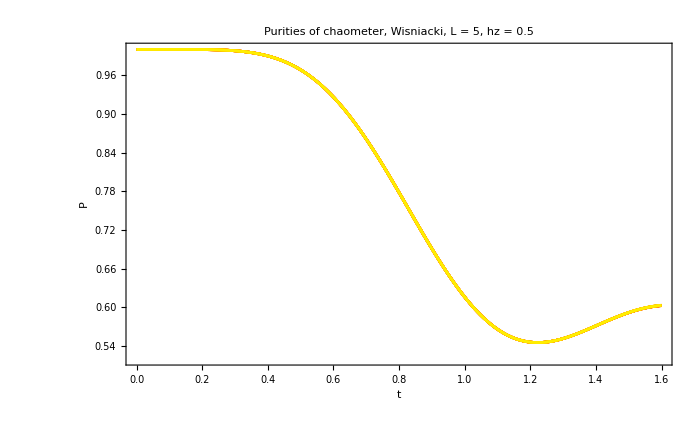

```mathematica
tlist=Range[0,tf,dt];
uno=ListPlot[Table[Transpose[{tlist,i}],{i,data}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of chaometer, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->Table[Directive[j,Opacity[0.35]],{j,coloursc}],PlotRange->All,ImageSize->700,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]}]
```

```mathematica
data2x={};
data2y={};
data2z={};
Do[
reducedmagax=Table[Chop[Tr[sx.i]],{i,data2[[k,All]]}];
reducedmagay=Table[Chop[Tr[sy.i]],{i,data2[[k,All]]}];
reducedmagaz=Table[Chop[Tr[sz.i]],{i,data2[[k,All]]}];
AppendTo[data2x,reducedmagax];
AppendTo[data2y,reducedmagay];
AppendTo[data2z,reducedmagaz];
,{k,ale2}];
```

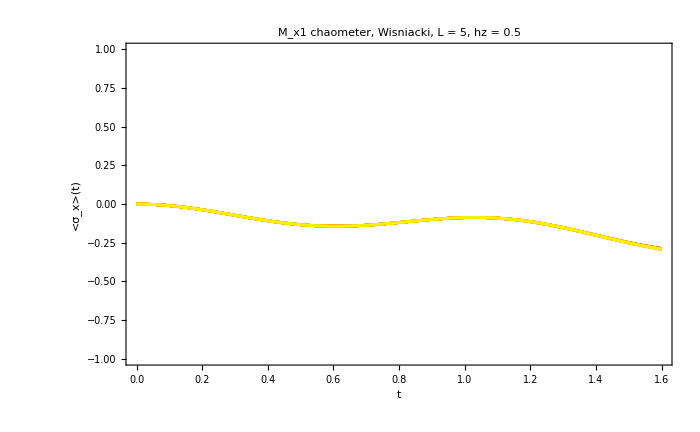

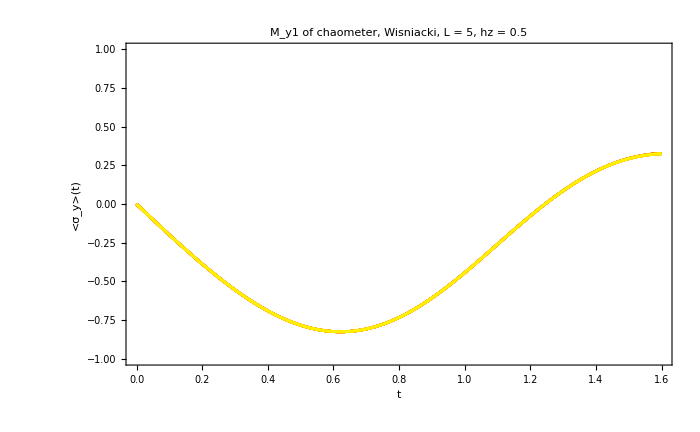

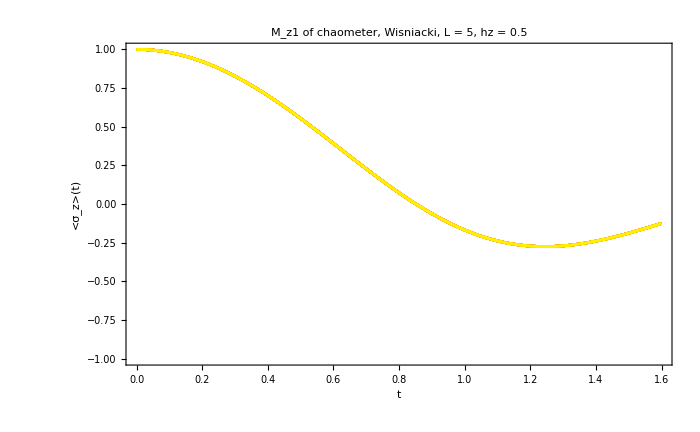

```mathematica
ListPlot[Table[Transpose[{tlist,k}],{k,data2x}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_x1 chaometer, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->Table[Directive[j,Opacity[0.4]],{j,coloursc}],PlotRange->{All,{-1,1}},ImageSize->700,PlotLegends->Style["M_x(t)",Black,25],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ_x>(t)"]}]
ListPlot[Table[Transpose[{tlist,k}],{k,data2y}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_y1 of chaometer, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->Table[Directive[j,Opacity[0.4]],{j,coloursc}],PlotRange->{All,{-1,1}},ImageSize->700,PlotLegends->Style["M_y(t)",Black,25],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ_y>(t)"]}]
ListPlot[Table[Transpose[{tlist,k}],{k,data2z}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of chaometer, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->Table[Directive[j,Opacity[0.4]],{j,coloursc}],PlotRange->{All,{-1,1}},ImageSize->700,PlotLegends->Style["M_z(t)",Black,25],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ_z>(t)"]}]
```

## Environment purities

```mathematica
ψat=Table[StateEvolution[t,j,eigenval,eigenvec],{j,ψa},{t,0,tf,dt}];
```

```mathematica
data={};
Do[
densitya=Table[Dyad[j,j],{j,ψat[[k,All]]}];
reduceda=Table[Chop[MatrixPartialTrace[i,1,{2,2^(L-1)}]],{i,densitya}];
puritiesa=Table[Chop[Purity[i]],{i,reduceda}];
AppendTo[data,puritiesa];
,{k,ale2}];
```

```mathematica
tlist=Range[0,tf,dt];
```

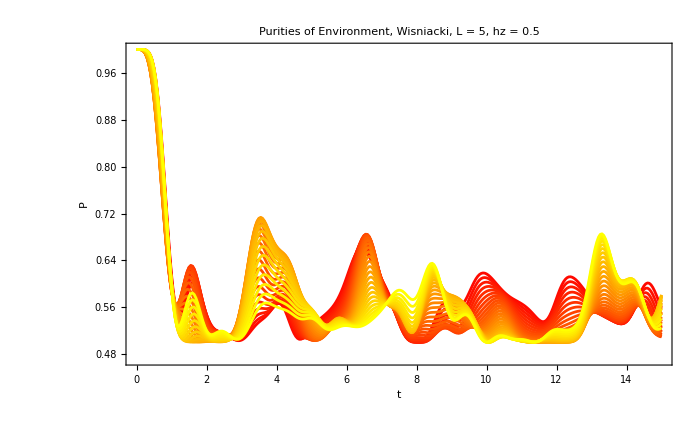

```mathematica
dos=ListPlot[Table[Transpose[{tlist,i}],{i,data}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of Environment, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->coloursc,PlotRange->All,ImageSize->700,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]}]
```

# Product states characterization

```mathematica
L=5;
hx=1;
J=1.;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
ipreigen=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
```

```mathematica
ale=2000;
caometer=Table[haar[1],{i,ale}];
```

```mathematica
ale2=30;
coloursc=Table[RGBColor[i,i/ale2,1-i],{i,ale2}];
(*coloursc=Table[RGBColor[1-i,i/ale2,1-i],{i,ale2}];*)
```

```mathematica
single=qubit[0,0];
```

```mathematica
(*blochtest=Table[qubit[i,0],{i,0,Pi,Pi/ale2}];*)
blochtest=Table[qubit[Pi/2,i],{i,0,2Pi,2Pi/(ale2-1)}];
```

```mathematica
scatterplots={};
scatterplots2c={};
ψec={};

Do[

ψTc=Flatten[KroneckerProduct[coherentstate[single,L-2],N[blochtest[[i]]]]];
(*caometer=Table[haar[1],{i,ale}];*)
(*ψTc=coherentstate[single,L-1];*)
(*ψTc=Flatten[KroneckerProduct[haar[1],coherentstate[qubit[Pi,0],L-2]]];*)
(*ψTc=Flatten[KroneckerProduct[Flatten[KroneckerProduct[haar[1],haar[1]]],coherentstate[qubit[0,0],L-3]]];*)
(*ψTc=RandomChainProductState[L-1];*)
AppendTo[ψec,ψTc];
ψc=ParallelTable[Flatten[KroneckerProduct[i,ψTc]],{i,caometer}];
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
energiesc=Table[Chop[Conjugate[i].H.i],{i,ψc}];

scatter1=ListPlot[Transpose[{energiesc,iprsc}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",35,Black],PlotStyle->{Directive[coloursc[[i]],Opacity[0.25]]},PlotRange->All,ImageSize->1000,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}];
AppendTo[scatterplots,scatter1];

iprsc=ParallelTable[Total[Abs[i]^4],{i,ψc}];
scatter2c=ListPlot[{Transpose[{energiesc,iprsc}],Transpose[{eigenval,ipreigen}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",35,Black],PlotStyle->{Directive[coloursc[[i]],Opacity[0.5]],Directive[Gray,Opacity[1]]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]},ImageSize->1000];
AppendTo[scatterplots2c,scatter2c];

,{i,ale2}];
```

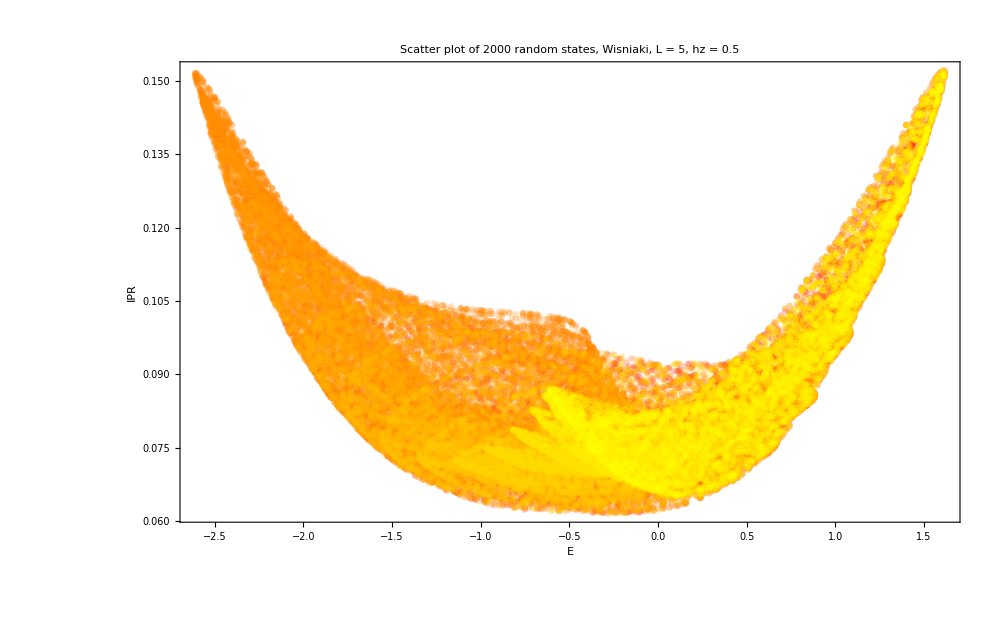

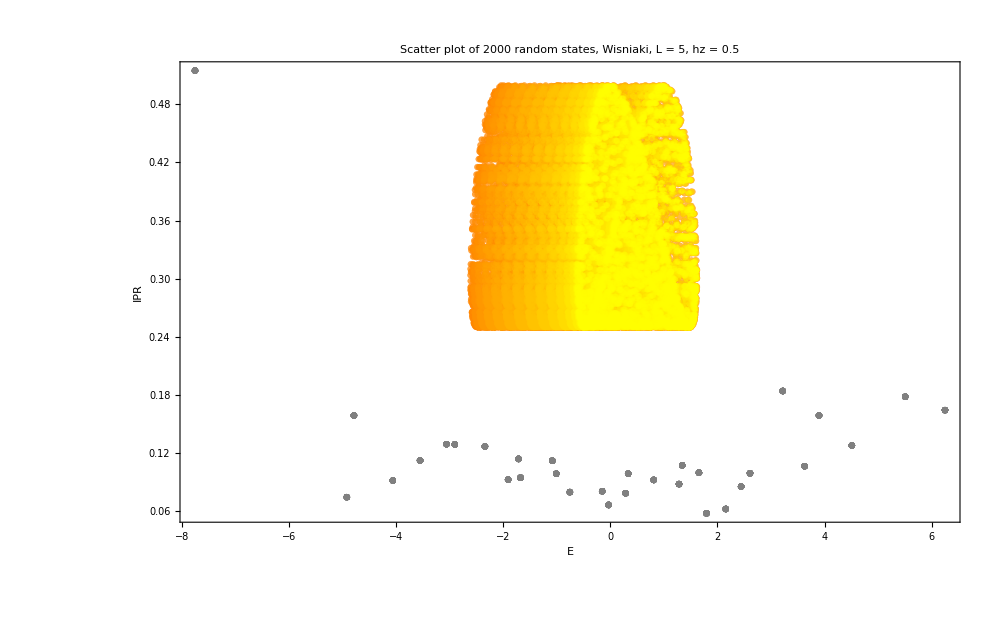

```mathematica
tres=Show[scatterplots,PlotRange->All]
cuatro=Show[scatterplots2c,PlotRange->All]
```

```mathematica
energyentropy=Table[Tr[(MatrixPartialTrace[Dyad[i],2,{2,2^(L-1)}])^2],{i,eigenvec}];
ListPlot[Transpose[{eigenval,energyentropy}],PlotRange->All];
```

```mathematica
a=ListPlot[{Transpose[{eigenval,energyentropy}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",35,Black],PlotStyle->{Directive[Brown,Opacity[0.5]],Directive[Gray,Opacity[1]]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]},ImageSize->1000];
Show[{scatterplots2c,a},PlotRange->All];
```

## Quantum channel

```mathematica
tf=1.6;
dt=0.005;
(*QUANTUM CHANNEL*)
ψe=ψec;
styles={Style["Random product state, L = "<>ToString[L]<>", hz = "<>ToString[hz],40,Black]};

(*For each initial state compute bloch sphere dynamics and export it as video*)
allchoieigenvalues={};
allchoipurities={};
spectrum={};

Do[

choiEigenvalues={};
choipurities={};

Do[
superOp=Superoperator[t,ψe[[i]],eigenval,eigenvec,L];
AppendTo[spectrum,Eigenvalues[superOp]];
AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];
AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];
,{t,0,tf,dt}];

AppendTo[allchoieigenvalues,
Chop[choiEigenvalues]];
AppendTo[allchoipurities,Chop[choipurities]];
,{i,Length[ψe]}];
```

```mathematica
limit=Plot[{0.5,0.25},{x,0,tf},PlotStyle->Directive[RGBColor[0.93,0.07,0.66],Dashed]];
enerpury=Plot[{energyentropy},{x,0,tf},PlotStyle->Directive[Brown,Opacity[0.05]]];
listplots={};
puritiesplots={};

Do[

AppendTo[listplots,
Show[{
ListPlot[Transpose[Chop[allchoieigenvalues[[i]]]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[coloursc[[i]],Opacity[0.15]],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","λ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000]
,limit}]];

AppendTo[puritiesplots,
Show[{
ListPlot[Chop[allchoipurities[[i]]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[coloursc[[i]],Opacity[0.5]],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000]
,limit}]];

,{i,Length[ψe]}];
```

```mathematica
plotmeanchoieigenval=ListPlot[Transpose[Chop[Mean[allchoieigenvalues]]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","λ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000];

plotmeanchoipurity=ListPlot[Chop[Mean[allchoipurities]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Black,Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000];
```

```mathematica
testimage=Grid[{{Show[{listplots,plotmeanchoieigenval}],Show[scatterplots2c,PlotRange->All]},{Show[{puritiesplots,plotmeanchoipurity},PlotRange->{{0,tf},All}],Show[{spectrumplots[[1]],spectrumplots[[-1]]}]}},Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["frame_blochtest_wisniacki_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>"_hx_"<>ToString[hx]<>"_excitation_fourth_"<>ToString[ale2]<>"_tf_"<>ToString[tf]<>".png",testimage];
```

## spectrum

```mathematica
tlist=Range[0,tf,dt];
newspectrum=ArrayReshape[spectrum,{ale2,Length[tlist],4}];
spectrumplots=Table[ComplexListPlot[newspectrum[[i]],PlotRange->{{-1.02,1.02},{-1.02,1.02}},PlotStyle->coloursc[[i]],PlotLabel->Style["Spectrum plot of Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>", tf = "<>ToString[tf],35,Black],ImageSize->1000,PlotTheme->"Detailed",GridLines->None,Frame->True,Axes->True],{i,Length[newspectrum]}];
```

```mathematica
Table[Export["spectrum_blochtest_fourths_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>"_hx_"<>ToString[hx]<>"_tf_"<>ToString[tf]<>"_enviroment_end_"<>ToString[i]<>".png",spectrumplots[[i]]],{i,ale2}]
```

```mathematica
Export["spectrum_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>"_tf_"<>ToString[tf]<>".mp4",spectrumplots,"FrameRate"->1]
```

```mathematica
tlist=Range[0,tf,dt];
newspectrum=spectrum[[1;;Length[tlist]]];
```

```mathematica
spectrumplots3=Table[ComplexListPlot[newspectrum[[;;i]],PlotRange->{{-1.02,1.02},{-1.02,1.02}},PlotStyle->Table[Blend[{LightRed,Red},j/(1.5*i)],{j,i}],PlotLabel->Style["Spectrum plot of Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>", tf = "<>ToString[tf]<>", t ="<>ToString[tlist[[i]]],35,Black],ImageSize->600,PlotTheme->"Detailed",GridLines->None,Frame->True,Axes->True],{i,1,321,20}];
```

```mathematica
ListAnimate[spectrumplots3,AnimationRunning->False]
```

```mathematica
Export["spectrum_blochtest_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>"_tf_"<>ToString[tf]<>".mp4",spectrumplots3,"FrameRate"->5]
```

spectrum_blochtest_L_5_hz_0.5_tf_1.6.mp4

## example

```mathematica
(*Example Trajectory*)trajectory=Table[{Cos[t],Sin[t]},{t,0,2 Pi,0.1}];

(*Generate frames with fading effect and highlighted current position*)
frames=Table[Show[ListPlot[trajectory[[;;i]],PlotStyle->Table[Blend[{Red,LightRed},j/i],{j,i}],Axes->True,PlotRange->{{-1.5,1.5},{-1.5,1.5}}],Graphics[{PointSize[Large],Red,Point[trajectory[[i]]]}]],{i,Length[trajectory]}];

(*Create an animation*)
ListAnimate[frames,AnimationRunning->False]
```

## Different size spectrums

```mathematica
spectrumplots=Table[Grid[{{spectrumplots3[[i]],spectrumplots4[[i]]},{spectrumplots5[[i]],spectrumplots6[[i]]}},Spacings->{5,5},Alignment->{Center,Center},Frame->All],{i,Length[tlist]}];
```

```mathematica
Table[Export["spectrum_L_3456_"<>ToString[L]<>"_hz_"<>ToString[hz]<>"_"<>ToString[i]<>".png",spectrumplots[[i]]],{i,Length[spectrumplots]}]
```

```mathematica
Export["spectrum_L_3456_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".mp4",spectrumplots,"FrameRate"->10]
```

Export::interr2: An unknown internal error occurred. Consult Internal`$LastInternalFailure for potential information.

$Failed

## Plotting as a function of t

```mathematica
tlist=Range[0,tf,dt];
newspectrum=spectrum[[1;;Length[tlist]]];
```

```mathematica
spectrumplots=Table[ComplexListPlot[newspectrum[[1;;i]],PlotRange->{{-1.02,1.02},{-1.02,1.02}},PlotStyle->coloursc[[1]],PlotLabel->Style["Spectrum plot of Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>", tf = "<>ToString[tf],35,Black],ImageSize->1000,PlotTheme->"Detailed",GridLines->None,Frame->True,Axes->True],{i,100}];
```

```mathematica
spectrumplots=Table[Grid[{{Show[{listplots,plotmeanchoieigenval}],Show[scatterplots2c,PlotRange->All]},{Show[{puritiesplots,plotmeanchoipurity},PlotRange->{{0,tf},All}],ComplexListPlot[newspectrum[[1;;i]],PlotRange->{{-1.02,1.02},{-1.02,1.02}},PlotStyle->coloursc[[1]],PlotLabel->Style["Spectrum plot of Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>", tf = "<>ToString[tf],35,Black],ImageSize->1000,PlotTheme->"Detailed",GridLines->None,Frame->True,Axes->True]}},Spacings->{5,5},Alignment->{Center,Center},Frame->All],{i,Length[tlist]}];
```

```mathematica
Export["spectrum_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".mp4",spectrumplots,"FrameRate"->10]
```

spectrum_L_5_hz_0.5.mp4

```mathematica
ListAnimate[spectrumplots,AnimationRunning->False]
```

## SP(t)

```mathematica
ψec//Dimensions
```

{10,64}

```mathematica
newψec=Table[Flatten[KroneckerProduct[haar[1],i]],{i,ψec}];
```

```mathematica
tlist=Range[0,tf,0.1];
ψct=Table[StateEvolution[t,j,eigenval,eigenvec],{j,newψec},{t,0,tf,0.1}];
```

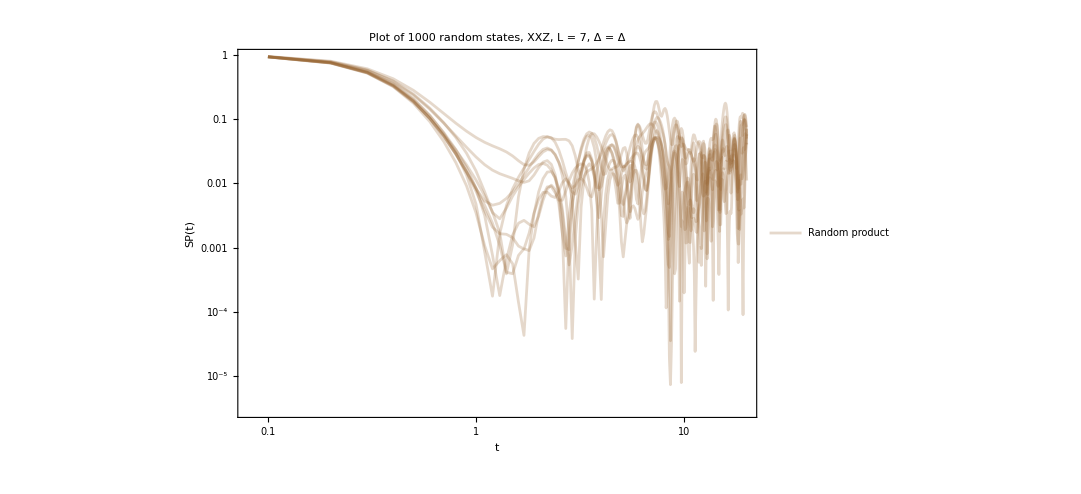

```mathematica
singlec=ListLogLogPlot[Table[{tlist[[i]],Abs[Conjugate[ψct[[j,1]]].ψct[[j,i]]]^2},{j,Length[ψct]},{i,Length[Range[0,tf,0.1]]}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Directive[Brown,Opacity[0.25]]},PlotRange->All,ImageSize->800,PlotLegends->{Style["Random product",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

# Sweep hz

```mathematica
ale=2000;
caometer=Table[haar[1],{i,ale}];
ale2=10;
coloursc=Table[RGBColor[i,i/ale2,1-i],{i,ale2}];
single=qubit[0,0];
tf=15.;
dt=0.025;
L=5;
hx=J=1.;
```

```mathematica
Do[

H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
ipreigen=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];

scatterplots={};
scatterplots2c={};
ψec={};

Do[
ψTc=Flatten[KroneckerProduct[coherentstate[single,L-2],haar[1]]];
AppendTo[ψec,ψTc];
ψc=ParallelTable[Flatten[KroneckerProduct[i,ψTc]],{i,caometer}];
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
energiesc=Table[Chop[Conjugate[i].H.i],{i,ψc}];
scatter1=ListPlot[Transpose[{energiesc,iprsc}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",35,Black],PlotStyle->{Directive[coloursc[[i]],Opacity[0.25]]},PlotRange->All,ImageSize->1000,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}];
AppendTo[scatterplots,scatter1];
iprsc=ParallelTable[Total[Abs[i]^4],{i,ψc}];
scatter2c=ListPlot[{Transpose[{energiesc,iprsc}],Transpose[{eigenval,ipreigen}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",35,Black],PlotStyle->{Directive[coloursc[[i]],Opacity[0.5]],Directive[Gray,Opacity[1]]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]},ImageSize->1000];
AppendTo[scatterplots2c,scatter2c];
,{i,ale2}];
Show[scatterplots,PlotRange->All];
Show[scatterplots2c,PlotRange->All];

(*QUANTUM CHANNEL*)
ψe=ψec;
styles={Style["Random product state, L = "<>ToString[L]<>", hz = "<>ToString[hz],40,Black]};
(*For each initial state compute bloch sphere dynamics and export it as video*)
allchoieigenvalues={};
allchoipurities={};
spectrum={};

Do[

choiEigenvalues={};
choipurities={};

Do[
superOp=Superoperator[t,ψe[[i]],eigenval,eigenvec,L];
AppendTo[spectrum,Eigenvalues[superOp]];
AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];
AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];
,{t,0,tf,dt}];

AppendTo[allchoieigenvalues,
Chop[choiEigenvalues]];
AppendTo[allchoipurities,Chop[choipurities]];
,{i,Length[ψe]}];

limit=Plot[0.25,{x,0,tf},PlotStyle->Directive[RGBColor[0.93,0.07,0.66],Dashed]];
listplots={};
puritiesplots={};

Do[

AppendTo[listplots,
Show[{
ListPlot[Transpose[Chop[allchoieigenvalues[[i]]]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[coloursc[[i]],Opacity[0.15]],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","λ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000]
,limit}]];

AppendTo[puritiesplots,
Show[{
ListPlot[Chop[allchoipurities[[i]]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[coloursc[[i]],Opacity[0.5]],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000]
,limit}]];

,{i,Length[ψe]}];

plotmeanchoieigenval=ListPlot[Transpose[Chop[Mean[allchoieigenvalues]]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","λ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000];

plotmeanchoipurity=ListPlot[Chop[Mean[allchoipurities]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Black,Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000];

tlist=Range[0,tf,dt];
newspectrum=ArrayReshape[spectrum,{10,Length[tlist],4}];
spectrumplots=Table[ComplexListPlot[newspectrum[[i]],PlotRange->{{-1.02,1.02},{-1.02,1.02}},PlotStyle->coloursc[[i]],PlotLabel->Style["Spectrum plot of Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>", tf = "<>ToString[tf],35,Black],ImageSize->1000,PlotTheme->"Detailed",GridLines->None,Frame->True,Axes->True],{i,Length[newspectrum]}];
testimage=Grid[{{Show[{listplots,plotmeanchoieigenval}],Show[scatterplots2c,PlotRange->All]},{Show[{puritiesplots,plotmeanchoipurity},PlotRange->{{0,tf},All}],spectrumplots[[1]]}},Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["frame_wisniacki_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>"_zeroenviroment_excitationatend_"<>ToString[ale2]<>"_.png",testimage,ImageResolution->300];


,{hz,0,3,0.01}]
```

$Aborted